ⅈ ⅇ^(-ⅈ x)-ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-2 ⅈ x)+1/2 ⅈ ⅇ^(2 ⅈ x)+1/3 ⅈ ⅇ^(-3 ⅈ x)-1/3 ⅈ ⅇ^(3 ⅈ x)-1/4 ⅈ ⅇ^(-4 ⅈ x)+1/4 ⅈ ⅇ^(4 ⅈ x)+1/5 ⅈ ⅇ^(-5 ⅈ x)-1/5 ⅈ ⅇ^(5 ⅈ x)-1/6 ⅈ ⅇ^(-6 ⅈ x)+1/6 ⅈ ⅇ^(6 ⅈ x)+1/7 ⅈ ⅇ^(-7 ⅈ x)-1/7 ⅈ ⅇ^(7 ⅈ x)

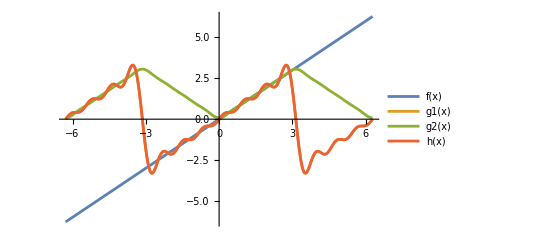

```mathematica
$Version;
f[x_]:= x
g2[x_]=FourierCosSeries[f[x],x,7];
g1[x_]=FourierSinSeries[f[x],x,7];
h[x_]=FourierSeries[f[x],x,7]
Plot[{f[x],g1[x],g2[x],h[x]},{x,-2π,2π},
PlotLegends->"Expressions"]
```